## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m"];Data=<|"Vertices List"->{1,2,3,4},"Adjacency Matrix"->{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1}},"Exit Vertices and Terminal Costs"->{{3,U1},{4,U2}},"Switching Costs"->{}|>;
d2e = Data2Equations[Data/.{I1->2,U1->10,U2->0}];
(crit =CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

Iterative boolean convert took 0.001039 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

{0.008723,Null}

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

At least one of the restrictions is True

EqEntryIn: True
j12==2

EqValueAuxiliaryEdges: True
u11==u12&&u7==u8&&u9==u10

EqCompCon: True
jt1==0&&(jt2==0||u1-u12==0)&&(jt3==0||-u2+u3==0)&&(jt4==0||-u2+u5==0)&&(jt5==0||u2-u3==0)&&(jt6==0||-u3+u5==0)&&(jt7==0||u2-u5==0)&&(jt8==0||u3-u5==0)&&(jt9==0||-u4+u7==0)&&jt10==0&&(jt11==0||-u6+u9==0)&&jt12==0

EqBalanceSplittingCurrents: True
j1==jt1&&j12==jt2&&j2==jt3+jt4&&j3==jt5+jt6&&j5==jt7+jt8&&j4==jt9&&j7==jt10&&j6==jt11&&j9==jt12

EqCurrentCompCon: True
(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)

EqTransitionCompCon: True
(jt1==0||jt2==0)&&(jt10==0||jt9==0)&&(jt11==0||jt12==0)&&(jt3==0||jt5==0)&&(jt4==0||jt7==0)&&(jt6==0||jt8==0)

EqPosJs: True
j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0

EqPosJts: True
jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0

EqSwitchingByVertex: True
u1≤∞&&u12≤u1&&u2≤u3&&u2≤u5&&u3≤u2&&u3≤u5&&u5≤u2&&u5≤u3&&u4≤u7&&u7≤∞&&u6≤u9&&u9≤∞

Nlhs: {0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6}

Nrhs: {4.16012,0.,4.16012}
{-j1+j2+IntM[-j1+j2,1->2],-j3+j4+IntM[-j3+j4,2->3],-j5+j6+IntM[-j5+j6,2->4]}

Max error for non-linear solution: 4.16012

<|u1→4.,u2→2.,u3→2.,u4→2.,u5→2.,u6→0.,u7→10.,u8→10.,u9→0.,u10→0.,u11→4.,u12→4.,j1→0.,j2→2.,j3→0.,j4→0.,j5→0.,j6→2.,j7→0.,j8→0.,j9→0.,j10→2.,j11→0.,j12→2.,jt1→0.,jt2→2.,jt3→0.,jt4→2.,jt5→0.,jt6→0.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→2.,jt12→0.|>

```mathematica
d2e["jvars"]/.%
```

<|{1,1->2}→0.,{2,1->2}→2.,{2,2->3}→0.,{3,2->3}→0.,{2,2->4}→0.,{4,2->4}→2.,{3,3->ex3}→0.,{ex3,3->ex3}→0.,{4,4->ex4}→0.,{ex4,4->ex4}→2.,{en1,en1->1}→0.,{1,en1->1}→2.|>

```mathematica
d2e["uvars"]/.%%
```

<|{1,1->2}→4.,{2,1->2}→2.,{2,2->3}→2.,{3,2->3}→2.,{2,2->4}→2.,{4,2->4}→0.,{3,3->ex3}→10.,{ex3,3->ex3}→10.,{4,4->ex4}→0.,{ex4,4->ex4}→0.,{en1,en1->1}→4.,{1,en1->1}→4.|>

### This is the correct solution, since the current should split equally!

```mathematica
d2e = Data2Equations[Data/.{I1->65,U1->45,U2->0}];
(crit =CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

Iterative boolean convert took 0.001754 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

<|j12→65,j11→0,j7→0,j9→0,j2→65,j1→0,j4→10,j6→55,j3→0,j8→10,j5→0,j10→55,u8→45,u10→0,jt10→0,jt11→55,jt12→0,jt2→65,jt4→55,jt5→0,jt6→0,jt8→0,jt9→10,u12→120,u7→45,u9→0,jt1→0,jt7→0,u11→120,u2→55,u5→55,u3→55,u4→45,u6→0,jt3→10,u1→120|>

{0.037509,Null}

```mathematica
crit["AssoCritical"]
```

<|u1→120,u2→55,u3→55,u4→45,u5→55,u6→0,u7→45,u8→45,u9→0,u10→0,u11→120,u12→120,j1→0,j2→65,j3→0,j4→10,j5→0,j6→55,j7→0,j8→10,j9→0,j10→55,j11→0,j12→65,jt1→0,jt2→65,jt3→10,jt4→55,jt5→0,jt6→0,jt7→0,jt8→0,jt9→10,jt10→0,jt11→55,jt12→0|>

### DataToEquations and the critical congestion solver

```mathematica
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"densitiy at "#,PlotRange-> {-.5,1.7}]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at "#,PlotRange-> {2,8}]&/@MFGEquations["BEL"]
```

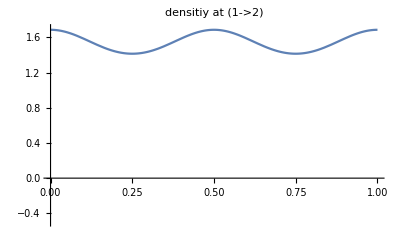
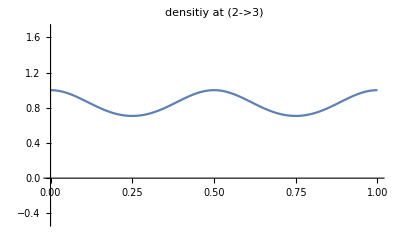
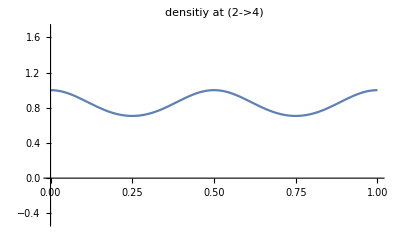

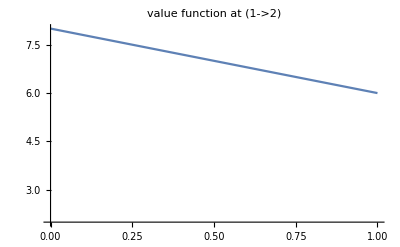
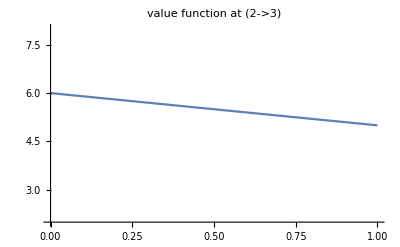
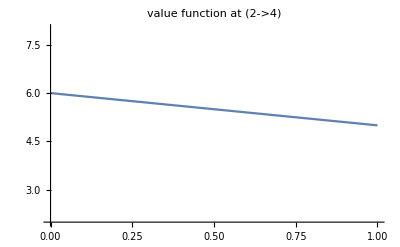

```mathematica
FFR=MFGEquations["criticalreduced1"][[2]];
Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, PlotLabel->"densitiy at "#,PlotRange-> {-.5,1.7}]&/@MFGEquations["BEL"]
Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, PlotLabel->"value function at "#,PlotRange-> {2,8}]&/@MFGEquations["BEL"]
```

```mathematica
1
```

1